```mathematica
Subscript[v, j][t_] := Subscript[bk, j] Subscript[s, j]/Subscript[l, j]*(e^{Subscript[l, j] t}-1)+Subscript[s, j] e^{-t}Subscript[y, j](e^{(Subscript[l, j]+1)t}-1)
l=.
v=.
s=.
b=.

DSolve[{v'[t]==l v[t]+s^2(l+1)*r[t]+s b ,r'[t]==-r[t],r[0]==y/s,v[0]==-s^2/2},{v[t],r[t]},t]
```

```mathematica
DSolve[{v'[t]== Exp[-t]*a + b,v[0]==c},v[t],t]
```

```mathematica
{{v[t]->ⅇ^-t (-a+a ⅇ^t+c ⅇ^t+b ⅇ^t t)}}

Simplify[ⅇ^-t (-a+a ⅇ^t+c ⅇ^t+b ⅇ^t t)]
```

{{v[t]→ⅇ^-t (-a+a ⅇ^t+c ⅇ^t+b ⅇ^t t)}}

```mathematica
a:=(k+.5)*(q - d^2)
c:=-d^2/2
b:=k d
```

```mathematica
Solve[-c==a+c-a ⅇ^-t+b t,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→(1.5 d^2+1. d^2 k-0.5 q-1. k q+1. d k ProductLog[-(1. ⅇ^(-(1. (1.5 d^2+d^2 k-0.5 q-1. k q))/(d k)) (0.5 d^2+1. d^2 k-0.5 q-1. k q))/(d k)])/(d k)}}

```mathematica
Simplify[1/(d k)(1.5 d^2+1. d^2 k-0.5 q-1. k q+1. d k ProductLog[-(1. ⅇ^(-(1. (1.5 d^2+d^2 k-0.5 q-1. k q))/(d k)) (0.5 d^2+1. d^2 k-0.5 q-1. k q))/(d k)])]
```

(d^2 (1.5+1. k)+(-0.5-1. k) q)/(d k)+1. ProductLog[(ⅇ^((d^2 (-1.5-1. k)+(0.5+1. k) q)/(d k)) (d^2 (-0.5-1. k)+(0.5+1. k) q))/(d k)]

```mathematica
{{t->(-a-2 c+b ProductLog[(a ⅇ^(a/b+(2 c)/b))/b])/b}}

Simplify[(-a-2 c+b ProductLog[(a ⅇ^(a/b+(2 c)/b))/b])/b]
```

{{t→(-a-2 c+b ProductLog[(a ⅇ^(a/b+(2 c)/b))/b])/b}}

(-a-2 c+b ProductLog[(a ⅇ^((a+2 c)/b))/b])/b

```mathematica
DSolve[{v'[t]== Exp[-t]*(k+1/2)*d*(A-1)*d+k*d ,v[0]==-d^2/2},v[t],t]
```

{{v[t]→1/2 d ⅇ^-t (d-A d-2 d ⅇ^t+A d ⅇ^t+2 d k-2 A d k-2 d ⅇ^t k+2 A d ⅇ^t k+2 ⅇ^t k t)}}

```mathematica
Simplify[1/2 d ⅇ^-t (d-A d-2 d ⅇ^t+A d ⅇ^t+2 d k-2 A d k-2 d ⅇ^t k+2 A d ⅇ^t k+2 ⅇ^t k t)]
```

1/2 d^2 ⅇ^-t (1+2 k-2 ⅇ^t (1+k)+A (-1+ⅇ^t) (1+2 k))+d k t

```mathematica
Simplify[1/2 ⅇ^-t (-2 d^2+d^2 ⅇ^t+2 ⅇ^t kd t)]
```

d^2 (1/2-ⅇ^-t)+kd t

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→Log[-(l (-bs/l-s^2/2))/bs]/(l Log[e])}}

```mathematica
t =.
Simplify[s^2/2==b s/l(e^{l t}-1)*(1 + (y)/(b)*(e^{t}-1)/(t e^{t}))]
```

s^2/2=={((-1+e^(l t)) s (b t+y-e^-t y))/(l t)}

```mathematica
$Assumptions = t >0&&l<0&&s>0
```

t>0&&l<0&&s>0

```mathematica
t>0&&l<0
```

```mathematica
Simplify[s*e^{-t}*y*(e^{(l+1)t}-1)*(1+b/y*(t*e^t)/(e^t-1))]
```

```mathematica
{Exp[-t] (-1+e^((1+l) t)) s (1+(b e^t t)/((-1+e^t) y)) y}

$Assumptions=t>0
```

{(-1+e^((1+l) t)) ⅇ^-t s (1+(b e^t t)/((-1+e^t) y)) y}

t>0

```mathematica
Solve[s/2 ==b*t+y*(1-Exp[-t]),t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→(s-2 y+2 b ProductLog[(ⅇ^(-(s/2-y)/b) y)/b])/(2 b)}}

```mathematica
Simplify[t==(s-2 y+2 b ProductLog[(ⅇ^(-(s/2-y)/b) y)/b])/(2 b)]
```

t==(s-2 y+2 b ProductLog[(ⅇ^(-(s-2 y)/(2 b)) y)/b])/(2 b)

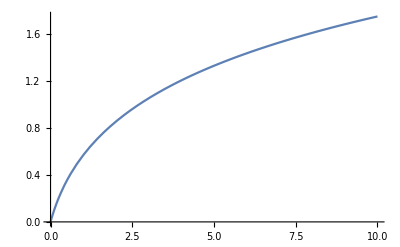

```mathematica
Plot[ProductLog[t],{t,0,10}]
```

```mathematica
Solve[-p==1 / (Log[(2*b/s-1) /(2*b/s+1)]), b]
```

{{b→ConditionalExpression[(-s-ⅇ^(-1/p) s)/(2 (-1+ⅇ^(-1/p))),-π≤Im[1/p]<π]}}

```mathematica
{{b->ConditionalExpression[((1+ⅇ^(1/p)) s)/(2 (-1+ⅇ^(1/p))),-π<Im[1/p]≤π]}}
```

{{b→ConditionalExpression[((1+ⅇ^(1/p)) s)/(2 (-1+ⅇ^(1/p))),-π<Im[1/p]≤π]}}

```mathematica
Simplify[b^2-2*p*b*s+p*s^2/2*(1+e^{-1/p})/(1-e^{-1/p})]
```

```mathematica
Simplify[1/(1+1/(b*k/(l*s))-1/2)]
```

General::munfl: Exp[-980.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

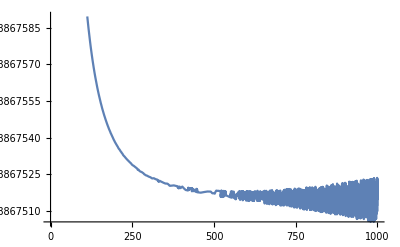

```mathematica
Plot[Sqrt[.25*((1+Exp[-1/p])/(1-Exp[-1/p]))^2-.5*p*((1+Exp[-1/p])/(1-Exp[-1/p]))],{p, 10^-3, 10^3}]
```

```mathematica
Solve[1==1/Log[(1 + 1/(b-.5))],b]

1/e
```

{{b→1.08198}}

1/e

```mathematica
y =1
l=-1
s=1
b=.
```

```mathematica
We g
```

1

-1

1

```mathematica
v[t]==-(ⅇ^-t s (2 b ⅇ^t-2 b ⅇ^(t+l t)+ⅇ^(t+l t) l s+2 l y-2 ⅇ^(t+l t) l y))/(2 l)
```

Unset::norep: Assignment on v for v[t] not found.

```mathematica
Plot[{-(ⅇ^-t s (2 b ⅇ^t-2 b ⅇ^(t+l t)+ⅇ^(t+l t) l s+2 l y-2 ⅇ^(t+l t) l y))/(2 l)/.b->1,s^2/2, -(ⅇ^-t s (2 b ⅇ^t-2 b ⅇ^(t+l t)+ⅇ^(t+l t) l s+2 l y-2 ⅇ^(t+l t) l y))/(2 l)/.b->1/4},{t,0,10},PlotLabels->{StringForm["((βk)_j)/σ_j = ``",b/Abs[l]/s/.b->1],"σ_j/2"}]
```

-Graphics-